# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"Washington"};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-02-07

```mathematica
states=Union[seqData[[All,2]]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Hawaii,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Hawaii,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Alabama→{{2022-01-24,37},{2022-01-25,37},{2022-01-26,27},{2022-01-27,14},{2022-01-28,28},{2022-01-29,30},{2022-01-30,32},{2022-01-31,16},{2022-02-01,9},{2022-02-02,12},{2022-02-03,11},{2022-02-04,3},{2022-02-05,0},{2022-02-06,0},{2022-02-07,0}},Arizona→{{2022-01-24,582},{2022-01-25,540},{2022-01-26,571},{2022-01-27,492},{2022-01-28,410},{2022-01-29,237},{2022-01-30,152},{2022-01-31,320},{2022-02-01,261},{2022-02-02,267},{2022-02-03,160},{2022-02-04,158},{2022-02-05,70},{2022-02-06,53},{2022-02-07,125}},Arkansas→{{2022-01-24,146},{2022-01-25,110},{2022-01-26,122},{2022-01-27,55},{2022-01-28,53},{2022-01-29,17},{2022-01-30,3},{2022-01-31,19},{2022-02-01,15},{2022-02-02,17},{2022-02-03,0},{2022-02-04,2},{2022-02-05,0},{2022-02-06,0},{2022-02-07,0}},California→{{2022-01-24,1263},{2022-01-25,1239},{2022-01-26,453},{2022-01-27,340},{2022-01-28,361},{2022-01-29,1944},{2022-01-30,1009},{2022-01-31,1077},{2022-02-01,935},{2022-02-02,647},{2022-02-03,162},{2022-02-04,1083},{2022-02-05,289},{2022-02-06,521},{2022-02-07,355}},Colorado→{{2022-01-24,332},{2022-01-25,197},{2022-01-26,370},{2022-01-27,661},{2022-01-28,252},{2022-01-29,344},{2022-01-30,73},{2022-01-31,310},{2022-02-01,92},{2022-02-02,26},{2022-02-03,29},{2022-02-04,37},{2022-02-05,0},{2022-02-06,0},{2022-02-07,1}},Connecticut→{{2022-01-24,273},{2022-01-25,183},{2022-01-26,167},{2022-01-27,200},{2022-01-28,194},{2022-01-29,9},{2022-01-30,92},{2022-01-31,197},{2022-02-01,85},{2022-02-02,59},{2022-02-03,70},{2022-02-04,68},{2022-02-05,28},{2022-02-06,24},{2022-02-07,12}},Delaware→{{2022-01-24,32},{2022-01-25,45},{2022-01-26,27},{2022-01-27,32},{2022-01-28,19},{2022-01-29,7},{2022-01-30,15},{2022-01-31,22},{2022-02-01,22},{2022-02-02,9},{2022-02-03,12},{2022-02-04,4},{2022-02-05,0},{2022-02-06,1},{2022-02-07,0}},Florida→{{2022-01-24,271},{2022-01-25,180},{2022-01-26,198},{2022-01-27,203},{2022-01-28,117},{2022-01-29,396},{2022-01-30,35},{2022-01-31,44},{2022-02-01,136},{2022-02-02,157},{2022-02-03,16},{2022-02-04,30},{2022-02-05,14},{2022-02-06,13},{2022-02-07,12}},Georgia→{{2022-01-24,132},{2022-01-25,251},{2022-01-26,252},{2022-01-27,445},{2022-01-28,286},{2022-01-29,150},{2022-01-30,42},{2022-01-31,110},{2022-02-01,91},{2022-02-02,95},{2022-02-03,15},{2022-02-04,26},{2022-02-05,0},{2022-02-06,0},{2022-02-07,0}},Hawaii→{{2022-01-24,68},{2022-01-25,43},{2022-01-26,63},{2022-01-27,68},{2022-01-28,41},{2022-01-29,37},{2022-01-30,27},{2022-01-31,54},{2022-02-01,27},{2022-02-02,37},{2022-02-03,37},{2022-02-04,15},{2022-02-05,2},{2022-02-06,0},{2022-02-07,0}},Illinois→{{2022-01-24,97},{2022-01-25,155},{2022-01-26,132},{2022-01-27,61},{2022-01-28,43},{2022-01-29,100},{2022-01-30,48},{2022-01-31,59},{2022-02-01,108},{2022-02-02,19},{2022-02-03,22},{2022-02-04,15},{2022-02-05,1},{2022-02-06,7},{2022-02-07,10}},Indiana→{{2022-01-24,79},{2022-01-25,63},{2022-01-26,129},{2022-01-27,102},{2022-01-28,57},{2022-01-29,84},{2022-01-30,34},{2022-01-31,43},{2022-02-01,49},{2022-02-02,32},{2022-02-03,14},{2022-02-04,6},{2022-02-05,10},{2022-02-06,6},{2022-02-07,78}},Kentucky→{{2022-01-24,34},{2022-01-25,16},{2022-01-26,77},{2022-01-27,201},{2022-01-28,46},{2022-01-29,13},{2022-01-30,9},{2022-01-31,13},{2022-02-01,21},{2022-02-02,8},{2022-02-03,16},{2022-02-04,35},{2022-02-05,6},{2022-02-06,4},{2022-02-07,59}},Louisiana→{{2022-01-24,100},{2022-01-25,49},{2022-01-26,128},{2022-01-27,58},{2022-01-28,119},{2022-01-29,32},{2022-01-30,8},{2022-01-31,12},{2022-02-01,44},{2022-02-02,106},{2022-02-03,69},{2022-02-04,38},{2022-02-05,7},{2022-02-06,0},{2022-02-07,20}},Maryland→{{2022-01-24,44},{2022-01-25,64},{2022-01-26,95},{2022-01-27,80},{2022-01-28,48},{2022-01-29,55},{2022-01-30,44},{2022-01-31,59},{2022-02-01,40},{2022-02-02,37},{2022-02-03,28},{2022-02-04,29},{2022-02-05,2},{2022-02-06,3},{2022-02-07,1}},Massachusetts→{{2022-01-24,1369},{2022-01-25,983},{2022-01-26,858},{2022-01-27,794},{2022-01-28,617},{2022-01-29,28},{2022-01-30,322},{2022-01-31,448},{2022-02-01,458},{2022-02-02,487},{2022-02-03,700},{2022-02-04,262},{2022-02-05,220},{2022-02-06,16},{2022-02-07,2}},Michigan→{{2022-01-24,115},{2022-01-25,78},{2022-01-26,119},{2022-01-27,69},{2022-01-28,58},{2022-01-29,110},{2022-01-30,73},{2022-01-31,41},{2022-02-01,52},{2022-02-02,35},{2022-02-03,22},{2022-02-04,8},{2022-02-05,0},{2022-02-06,0},{2022-02-07,1}},Minnesota→{{2022-01-24,74},{2022-01-25,48},{2022-01-26,53},{2022-01-27,314},{2022-01-28,44},{2022-01-29,149},{2022-01-30,34},{2022-01-31,46},{2022-02-01,140},{2022-02-02,31},{2022-02-03,16},{2022-02-04,23},{2022-02-05,6},{2022-02-06,18},{2022-02-07,96}},Nebraska→{{2022-01-24,188},{2022-01-25,172},{2022-01-26,107},{2022-01-27,74},{2022-01-28,53},{2022-01-29,45},{2022-01-30,42},{2022-01-31,62},{2022-02-01,36},{2022-02-02,32},{2022-02-03,41},{2022-02-04,17},{2022-02-05,4},{2022-02-06,0},{2022-02-07,33}},Nevada→{{2022-01-24,88},{2022-01-25,135},{2022-01-26,94},{2022-01-27,210},{2022-01-28,75},{2022-01-29,48},{2022-01-30,18},{2022-01-31,121},{2022-02-01,99},{2022-02-02,84},{2022-02-03,72},{2022-02-04,30},{2022-02-05,4},{2022-02-06,6},{2022-02-07,55}},New Hampshire→{{2022-01-24,136},{2022-01-25,51},{2022-01-26,30},{2022-01-27,59},{2022-01-28,76},{2022-01-29,9},{2022-01-30,20},{2022-01-31,42},{2022-02-01,30},{2022-02-02,28},{2022-02-03,27},{2022-02-04,29},{2022-02-05,5},{2022-02-06,0},{2022-02-07,0}},New Jersey→{{2022-01-24,45},{2022-01-25,127},{2022-01-26,428},{2022-01-27,230},{2022-01-28,83},{2022-01-29,11},{2022-01-30,16},{2022-01-31,49},{2022-02-01,67},{2022-02-02,208},{2022-02-03,119},{2022-02-04,15},{2022-02-05,47},{2022-02-06,34},{2022-02-07,4}},New Mexico→{{2022-01-24,36},{2022-01-25,89},{2022-01-26,114},{2022-01-27,114},{2022-01-28,105},{2022-01-29,40},{2022-01-30,17},{2022-01-31,19},{2022-02-01,42},{2022-02-02,20},{2022-02-03,12},{2022-02-04,1},{2022-02-05,0},{2022-02-06,2},{2022-02-07,0}},New York→{{2022-01-24,420},{2022-01-25,370},{2022-01-26,384},{2022-01-27,403},{2022-01-28,285},{2022-01-29,59},{2022-01-30,91},{2022-01-31,207},{2022-02-01,221},{2022-02-02,247},{2022-02-03,235},{2022-02-04,170},{2022-02-05,119},{2022-02-06,92},{2022-02-07,0}},North Carolina→{{2022-01-24,439},{2022-01-25,350},{2022-01-26,390},{2022-01-27,311},{2022-01-28,262},{2022-01-29,62},{2022-01-30,45},{2022-01-31,96},{2022-02-01,92},{2022-02-02,141},{2022-02-03,64},{2022-02-04,78},{2022-02-05,42},{2022-02-06,9},{2022-02-07,0}},North Dakota→{{2022-01-24,90},{2022-01-25,57},{2022-01-26,21},{2022-01-27,40},{2022-01-28,100},{2022-01-29,41},{2022-01-30,55},{2022-01-31,37},{2022-02-01,41},{2022-02-02,95},{2022-02-03,28},{2022-02-04,10},{2022-02-05,0},{2022-02-06,0},{2022-02-07,0}},Ohio→{{2022-01-24,120},{2022-01-25,139},{2022-01-26,184},{2022-01-27,209},{2022-01-28,106},{2022-01-29,31},{2022-01-30,36},{2022-01-31,65},{2022-02-01,67},{2022-02-02,50},{2022-02-03,6},{2022-02-04,0},{2022-02-05,1},{2022-02-06,1},{2022-02-07,3}},Oklahoma→{{2022-01-24,56},{2022-01-25,52},{2022-01-26,26},{2022-01-27,27},{2022-01-28,47},{2022-01-29,10},{2022-01-30,4},{2022-01-31,17},{2022-02-01,18},{2022-02-02,7},{2022-02-03,1},{2022-02-04,7},{2022-02-05,0},{2022-02-06,0},{2022-02-07,0}},Oregon→{{2022-01-24,71},{2022-01-25,114},{2022-01-26,125},{2022-01-27,73},{2022-01-28,91},{2022-01-29,33},{2022-01-30,41},{2022-01-31,89},{2022-02-01,82},{2022-02-02,48},{2022-02-03,42},{2022-02-04,18},{2022-02-05,10},{2022-02-06,3},{2022-02-07,1}},Pennsylvania→{{2022-01-24,124},{2022-01-25,175},{2022-01-26,210},{2022-01-27,272},{2022-01-28,124},{2022-01-29,131},{2022-01-30,50},{2022-01-31,33},{2022-02-01,71},{2022-02-02,119},{2022-02-03,60},{2022-02-04,25},{2022-02-05,12},{2022-02-06,3},{2022-02-07,2}},South Carolina→{{2022-01-24,21},{2022-01-25,71},{2022-01-26,100},{2022-01-27,165},{2022-01-28,137},{2022-01-29,9},{2022-01-30,19},{2022-01-31,29},{2022-02-01,14},{2022-02-02,22},{2022-02-03,23},{2022-02-04,27},{2022-02-05,0},{2022-02-06,0},{2022-02-07,0}},Tennessee→{{2022-01-24,73},{2022-01-25,57},{2022-01-26,64},{2022-01-27,159},{2022-01-28,117},{2022-01-29,66},{2022-01-30,92},{2022-01-31,92},{2022-02-01,54},{2022-02-02,16},{2022-02-03,18},{2022-02-04,36},{2022-02-05,2},{2022-02-06,5},{2022-02-07,5}},Texas→{{2022-01-24,217},{2022-01-25,287},{2022-01-26,471},{2022-01-27,454},{2022-01-28,324},{2022-01-29,384},{2022-01-30,386},{2022-01-31,417},{2022-02-01,395},{2022-02-02,249},{2022-02-03,70},{2022-02-04,60},{2022-02-05,48},{2022-02-06,115},{2022-02-07,60}},Utah→{{2022-01-24,320},{2022-01-25,214},{2022-01-26,199},{2022-01-27,229},{2022-01-28,201},{2022-01-29,87},{2022-01-30,24},{2022-01-31,131},{2022-02-01,75},{2022-02-02,151},{2022-02-03,50},{2022-02-04,207},{2022-02-05,114},{2022-02-06,6},{2022-02-07,74}},Vermont→{{2022-01-24,171},{2022-01-25,97},{2022-01-26,120},{2022-01-27,31},{2022-01-28,111},{2022-01-29,126},{2022-01-30,10},{2022-01-31,186},{2022-02-01,108},{2022-02-02,108},{2022-02-03,112},{2022-02-04,79},{2022-02-05,19},{2022-02-06,0},{2022-02-07,0}},Virginia→{{2022-01-24,18},{2022-01-25,99},{2022-01-26,240},{2022-01-27,48},{2022-01-28,10},{2022-01-29,18},{2022-01-30,17},{2022-01-31,14},{2022-02-01,19},{2022-02-02,72},{2022-02-03,50},{2022-02-04,6},{2022-02-05,0},{2022-02-06,0},{2022-02-07,1}},Wisconsin→{{2022-01-24,145},{2022-01-25,141},{2022-01-26,217},{2022-01-27,151},{2022-01-28,134},{2022-01-29,121},{2022-01-30,87},{2022-01-31,136},{2022-02-01,88},{2022-02-02,60},{2022-02-03,41},{2022-02-04,30},{2022-02-05,8},{2022-02-06,15},{2022-02-07,14}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

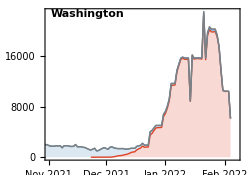

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

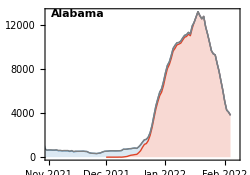
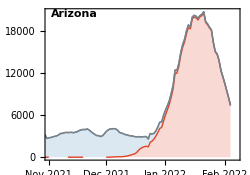
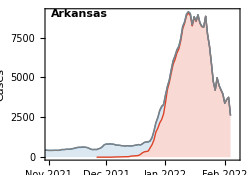
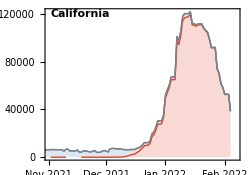
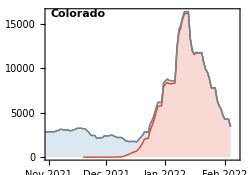
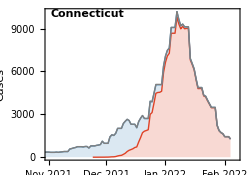
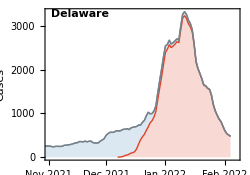
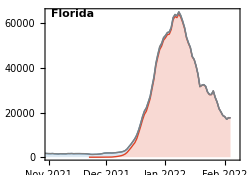
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png